## Beispiel gedämpftes Newton-Verfahren

#### Definition der Funktion:

```mathematica
f[x_,x0_,σ_]:=Sign[x-x0](1-E^(-Abs[(x-x0)]/σ))
```

Lösung der Gleichung f(x,x_0)=0 ist gegeben durch x_0. Für das Beispiel sei x_0=0.2, σ_0=0.1:

```mathematica
x0=0.2;σ0=0.1;
```

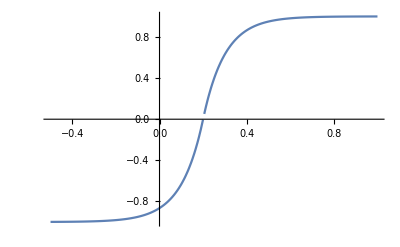

```mathematica
Plot[f[x,x0,σ0],{x,-.5,1},PlotRange->All]
```

#### Ableitung von f(x)

Für x≥x_0:

```mathematica
D[-(1-E^(-(x0-x)/σ)), x]
```

ⅇ^(-(0.2-x)/σ)/σ

Für x<x_0:

```mathematica
D[(1-E^(-(x-x0)/σ)), x]
```

ⅇ^(-(-0.2+x)/σ)/σ

Somit folgt für alle x∈ℝ:

```mathematica
df[x_,x0_,σ_]:=1/σ E^(-Abs[x-x0]/σ)
```

#### Newton-Verfahren

Das Newton-Verfahren konvergiert nur auf einem kleinen Intervall um x_0.

```mathematica
sol1=NestList[#-(df[#,x0,σ0])^-1 f[#,x0,σ0]&,0.33,10]
```

General::unfl: Underflow occurred in computation.

{0.33,0.0630703,0.356329,-0.0211203,0.791548,-36.1818,1.00991×10^157,Overflow[],Indeterminate,Indeterminate,Indeterminate}

```mathematica
sol1=Select[sol1,NumberQ[#]&&Abs[#]<$MaxNumber&]
```

{0.33,0.0630703,0.356329,-0.0211203,0.791548,-36.1818,1.00991×10^157}

Problem: der Funktionswert wird nicht kleiner:

```mathematica
Abs[f[sol1,x0,σ0]]
```

General::unfl: Underflow occurred in computation.

{0.727468,0.745714,0.790554,0.890431,0.997303,1.,Underflow[]+1}

```mathematica
sol=sol1;
Show[Plot[f[x,x0,σ0],{x,-.5,1}],Graphics[Line[Flatten[Transpose[Transpose/@{{sol,Table[0,{Length[sol]}]},{sol,f[sol,x0,σ0]}}],1]]]]
```

General::unfl: Underflow occurred in computation.

-Graphics-

#### Gedämpftes Newton-Verfahren

NewtonStep wird rekursiv mit dem Befehl NestList angewandt.

```mathematica
NewtonStep[x_,x0_,σ0_]:=Module[{λ,Cλ,s2,xn,sk,fk},
λ=1.;
Cλ=1-λ/4;
sk=df[x,x0,σ0]^-1 f[x,x0,σ0];
xn=x-λ sk;
s2=df[x,x0,σ0]^-1 f[xn,x0,σ0];
While[(Abs[s2]≥Cλ Abs[sk])&&(λ≥λmin),
λ=λ/2;
Cλ=1-λ/4;
xn=x-λ sk;
s2=df[x,x0,σ0]^-1 f[xn,x0,σ0];
];
AppendTo[output,{newtonStep++, "λ=",NumberForm[λ,{8,8}],"|f(x_k)| = ",Abs[f[xn,x0,σ0]],"|||f(x_(k + 1))||| = ",Abs[df[x,x0,σ0]^-1 f[xn,x0,σ0]],"|||f(x_k)||| = ",Abs[df[x,x0,σ0]^-1 f[x,x0,σ0]]}];
xn
]
```

```mathematica
λmin=10^-3;
```

In den ersten drei Newton-Schritten wird die Schrittweite gedämpft, das Verfahren konvergiert.

```mathematica
newtonStep=1;
output={};
sol2=NestList[NewtonStep[#,x0,σ0]&,1,20]
```

{1,-0.164046,0.299821,0.21415,0.19895,0.200006,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2}

```mathematica
output//TableForm
```

1 | λ= | 0.00390625 | |f(x_k)| =  | 0.97376 | |||f(x_(k + 1))||| =  | 290.274 | |||f(x_k)||| =  | 297.996
2 | λ= | 0.12500000 | |f(x_k)| =  | 0.631463 | |||f(x_(k + 1))||| =  | 2.40647 | |||f(x_k)||| =  | 3.71094
3 | λ= | 0.50000000 | |f(x_k)| =  | 0.131943 | |||f(x_(k + 1))||| =  | 0.0358019 | |||f(x_k)||| =  | 0.171343
4 | λ= | 1.00000000 | |f(x_k)| =  | 0.0104453 | |||f(x_(k + 1))||| =  | 0.0012033 | |||f(x_k)||| =  | 0.0151999
5 | λ= | 1.00000000 | |f(x_k)| =  | 0.0000553197 | |||f(x_(k + 1))||| =  | 5.59037×10^-6 | |||f(x_k)||| =  | 0.00105556
6 | λ= | 1.00000000 | |f(x_k)| =  | 1.53025×10^-9 | |||f(x_(k + 1))||| =  | 1.53033×10^-10 | |||f(x_k)||| =  | 5.53228×10^-6
7 | λ= | 1.00000000 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 1.53025×10^-10
8 | λ= | 0.00097656 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 0.
9 | λ= | 0.00097656 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 0.
10 | λ= | 0.00097656 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 0.
11 | λ= | 0.00097656 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 0.
12 | λ= | 0.00097656 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 0.
13 | λ= | 0.00097656 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 0.
14 | λ= | 0.00097656 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 0.
15 | λ= | 0.00097656 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 0.
16 | λ= | 0.00097656 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 0.
17 | λ= | 0.00097656 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 0.
18 | λ= | 0.00097656 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 0.
19 | λ= | 0.00097656 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 0.
20 | λ= | 0.00097656 | |f(x_k)| =  | 0. | |||f(x_(k + 1))||| =  | 0. | |||f(x_k)||| =  | 0.

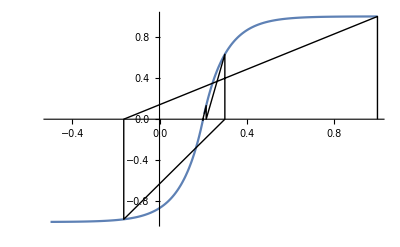

```mathematica
sol=sol2;
Show[Plot[f[x,x0,σ0],{x,-.5,1}],Graphics[Line[Flatten[Transpose[Transpose/@{{sol,Table[0,{Length[sol]}]},{sol,f[sol,x0,σ0]}}],1]]]]
```

#### Vergleich des Konvergenzverhaltens

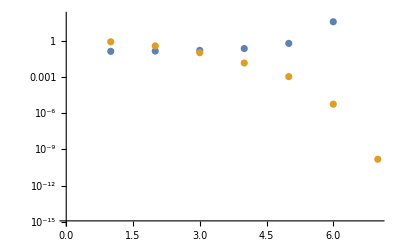

```mathematica
ListLogPlot[Abs[{sol1-x0,sol2-x0}],PlotRange->{10^-15,100}]
```